```mathematica
(*Standard Multi-Stream Potential Generation Code. The numerical equation of motion goes well for this potential. *)
φstep=0.02;m=10^-6;amp=100;φmax=30;α=0.01;
V[x_,y_]=1/2 m^2 x^2+1/2 m^2(y-φmax/2)^2+amp m^2 Exp[-α((x-φmax/2)^2+(y-φmax/2)^2)];
Plot3D[V[x,y],{x,0,φmax},{y,0,φmax},Mesh->None]
```

-Graphics3D-

```mathematica
(*Random Potential Generation Code. For φstep=0.1, amp=0.01, there are usually small bifurcations. For φstep=0.05, amp=0.01, there are usually large bifurcations. For φstep=0.2, amp=0.01, there are usually no bifurcations*)
φ1step=0.05;φ2step=0.05;m=10^-6;amp=0.001;φmax=30;
Vgen=Table[{{i,j},m^2/2(i*φ1step)^2(1+ amp Random[])},{i,0,φmax/φ1step},{j,0,φmax/φ2step}];

Vtmp=Interpolation[Flatten[Vgen,1]];
V[x_,y_]:=Vtmp[x/φ1step,y/φ2step];
Plot3D[V[x,y],{x,0,φmax},{y,0,φmax},Mesh->None]
```

-Graphics3D-

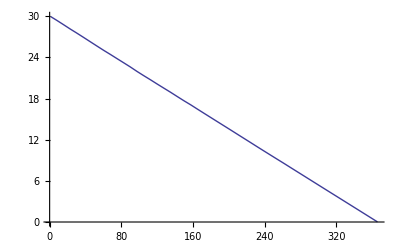

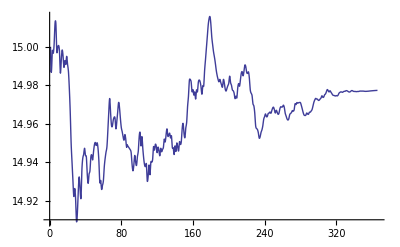

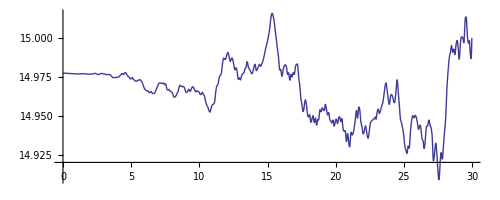

```mathematica
eternal=False;
φstart=φmax-φstep;
Δt=10^5;
steps=10^3;
Vp1[x1_,x2_]=D[V[x1,x2],x1];
Vp2[x1_,x2_]=D[V[x1,x2],x2];
H[x1_,x2_]=√(V[x1,x2]/3);
η:=RandomReal[NormalDistribution[0,1/√Δt]];
φ1=Table[0,{i,steps}];
φ2=Table[0,{i,steps}];
φ1[[1]]=φstart;
φ2[[1]]=φmax/2;
φ1[[2]]=φ1[[1]]-Δt/(3 H[φ1[[1]],φ2[[1]]])(Vp1[φ1[[1]],φ2[[1]]]);
φ2[[2]]=φ2[[1]]-Δt/(3 H[φ1[[1]],φ2[[1]]])(Vp2[φ1[[1]],φ2[[1]]]);
For[i=2,i<steps,i++,
φ1[[i+1]]=((2/Δt^2+(3H[φ1[[i]],φ2[[i]]])/Δt)φ1[[i]]-φ1[[i-1]]/Δt^2-(3 H[φ1[[i]],φ2[[i]]]^(5/2) η)/(2π)-Vp1[φ1[[i]],φ2[[i]]])/(1/Δt^2+(3H[φ1[[i]],φ2[[i]]])/Δt);φ2[[i+1]]=((2/Δt^2+(3H[φ1[[i]],φ2[[i]]])/Δt)φ2[[i]]-φ2[[i-1]]/Δt^2-(3 H[φ1[[i]],φ2[[i]]]^(5/2) η)/(2π)-Vp2[φ1[[i]],φ2[[i]]])/(1/Δt^2+(3H[φ1[[i]],φ2[[i]]])/Δt);
If[φ1[[i+1]]>φmax||φ2[[i+1]]>φmax||φ1[[i+1]]<0||φ2[[i+1]]<0,Break[]];
If[i-1/(Δt H[φ1[[i]],φ2[[i]]])>1, j=Round[i-1/(Δt H[φ1[[i]],φ2[[i]]])];If[(φ1[[j]]-φ1[[i]])^2+(φ2[[j]]-φ2[[i]])^2<H[φ1[[i]],φ2[[i]]]^2,eternal=True]]
];

φ1f=Interpolation[φ1];
φ2f=Interpolation[φ2];
plot1=Plot[φ1f[x],{x,1,i}, PlotRange->All]
plot2=Plot[φ2f[x],{x,1,i},PlotRange->All]
plot3=ParametricPlot[{φ1f[x],φ2f[x]},{x,1,i},PlotRange->All]
```